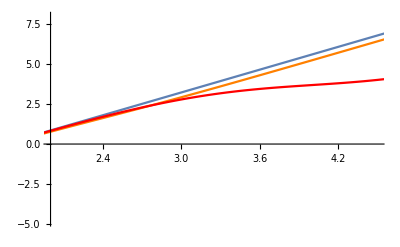

```mathematica
Block[
{qcrit,uz1,fu1,μextreme,dfu1,RGpu},
μextreme[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/uh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
qcrit[us_,uh_,μ_,z_,θ_]:=us^(θ/2-z)Sqrt[1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z))]/(μ (1-(us/uh)^(z-θ)));
uz1[q_,us_,uh_,μ_,z_,θ_]:=NDSolveValue[
{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) (((-2-z+θ) u[t]^(3-2 z) (u[t]/uh)^(z-θ))/uh^2-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(3-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(3-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)+(2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+((-((2+z-θ) (u[t]/uh)^(1+z-θ))/uh-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(1+2 z-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(1+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)) u'[t]^2)/(-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^(3-2 z) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]== us,u'[0]==0},u,{t,0.1,5.7},Method->"ExplicitRungeKutta"
];
fu1[t_,q_,us_,uh_,μ_,z_,θ_]:=uz1[q,us,uh,μ,z,θ][t];
dfu1[t_,q_,us_,uh_,μ_,z_,θ_]:=D[uz1[q,us,uh,μ,z,θ][t1],t1]/.{t1->t};
RGpu[t_,q_,us_,uh_,μ_,z_,θ_]:=Block[
{β,du,u,fu},
du=dfu1[t,q,us,uh,μ,z,θ];
u=fu1[t,q,us,uh,μ,z,θ];
fu=1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z));
β=1/(-((us/uh)^(1+z-θ) (2+z-θ))/uh+(uh^(-2 z+2 θ) us^(-1+2 (1+z-θ)) (1-(us/uh)^(-z+θ)) (z-θ) (1+z-θ) μ^2)/(2-θ)-(uh^(-1-2 z+2 θ) us^(2 (1+z-θ)) (us/uh)^(-1-z+θ) (z-θ) (-z+θ) μ^2)/(2 (2-θ)));
Return[β u^(θ/2-1)du/(fu Sqrt[u^(2(1-z))fu - du^2/fu])];
];
Show[
ListLinePlot[Table[{i,-(Abs[RGpu[i,0.85qcrit[0.1,1,0.75μextreme[1,1.5,0.5],1.5,0.5],0.1,1,0.75μextreme[1,1.5,0.5],1.5,0.5]]//Log)},{i,0.1,5,0.05}]],
ListLinePlot[Table[{i,-(Abs[RGpu[i,0.99qcrit[0.1,1,0.75μextreme[1,1.5,0.5],1.5,0.5],0.1,1,0.75μextreme[1,1.5,0.5],1.5,0.5]]//Log)},{i,0.1,5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,-(Abs[RGpu[i,0.998qcrit[0.1,1,0.75μextreme[1,1.5,0.5],1.5,0.5],0.1,1,0.75μextreme[1,1.5,0.5],1.5,0.5]]//Log)},{i,0.1,5,0.05}],PlotStyle->Red],
PlotRange->{{2,4.5},All},AxesOrigin->{2,0}
]
]
```

```mathematica
D[1-(u/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) u^(2(z-θ+1))/uh^(2z-2θ)(1-(u/uh)^(θ-z)),u]/.{u->us}
```

-((us/uh)^(1+z-θ) (2+z-θ))/uh+(uh^(-2 z+2 θ) us^(-1+2 (1+z-θ)) (1-(us/uh)^(-z+θ)) (z-θ) (1+z-θ) μ^2)/(2-θ)-(uh^(-1-2 z+2 θ) us^(2 (1+z-θ)) (us/uh)^(-1-z+θ) (z-θ) (-z+θ) μ^2)/(2 (2-θ))

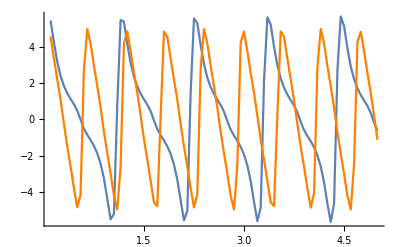

```mathematica
Block[
{qcrit,uz1,fu1,μextreme,dfu1,RGpu},
μextreme[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/uh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
qcrit[us_,uh_,μ_,z_,θ_]:=us^(θ/2-z)Sqrt[1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z))]/(μ (1-(us/uh)^(z-θ)));
uz1[q_,us_,uh_,μ_,z_,θ_]:=NDSolveValue[
{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) (((-2-z+θ) u[t]^(3-2 z) (u[t]/uh)^(z-θ))/uh^2-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(3-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(3-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)+(2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+((-((2+z-θ) (u[t]/uh)^(1+z-θ))/uh-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(1+2 z-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(1+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)) u'[t]^2)/(-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^(3-2 z) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]== us,u'[0]==0},u,{t,0.1,5.7}
];
fu1[t_,q_,us_,uh_,μ_,z_,θ_]:=uz1[q,us,uh,μ,z,θ][t];
dfu1[t_,q_,us_,uh_,μ_,z_,θ_]:=D[uz1[q,us,uh,μ,z,θ][t1],t1]/.{t1->t};
RGpu[t_,q_,us_,uh_,μ_,z_,θ_]:=Block[
{β,du,u,fu},
du=dfu1[t,q,us,uh,μ,z,θ];
u=fu1[t,q,us,uh,μ,z,θ];
fu=1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z));
β=1/(-((us/uh)^(1+z-θ) (2+z-θ))/uh+(uh^(-2 z+2 θ) us^(-1+2 (1+z-θ)) (1-(us/uh)^(-z+θ)) (z-θ) (1+z-θ) μ^2)/(2-θ)-(uh^(-1-2 z+2 θ) us^(2 (1+z-θ)) (us/uh)^(-1-z+θ) (z-θ) (-z+θ) μ^2)/(2 (2-θ)));
Return[u^(θ/2-1)du/(fu Sqrt[u^(2(1-z))fu - du^2/fu])];
];
Show[
ListLinePlot[Table[{i,Re[RGpu[i,1.4qcrit[0.1,1,0.75μextreme[1,1.5,0.5],1.5,0.5],0.1,1,0.75μextreme[1,1.5,0.5],1.5,0.5]]},{i,0.1,5,0.05}]],
ListLinePlot[Table[{i,Re[RGpu[i,2.1qcrit[0.1,1,0.75μextreme[1,1.5,0.5],1.5,0.5],0.1,1,0.75μextreme[1,1.5,0.5],1.5,0.5]]},{i,0.1,5,0.05}],PlotStyle->Orange],
PlotRange->{{0.1,5},All},AxesOrigin->{0,0}
]
]
```

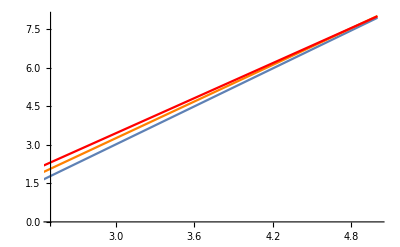

```mathematica
Block[
{qcrit,uz1,fu1,μextreme,dfu1,RGpu},
μextreme[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/uh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
qcrit[us_,uh_,μ_,z_,θ_]:=us^(θ/2-z)Sqrt[1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z))]/(μ (1-(us/uh)^(z-θ)));
uz1[q_,us_,uh_,μ_,z_,θ_]:=NDSolveValue[
{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) (((-2-z+θ) u[t]^(3-2 z) (u[t]/uh)^(z-θ))/uh^2-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(3-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(3-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)+(2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+((-((2+z-θ) (u[t]/uh)^(1+z-θ))/uh-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(1+2 z-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(1+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)) u'[t]^2)/(-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^(3-2 z) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]== us,u'[0]==0},u,{t,0.1,5.7},Method->"ExplicitRungeKutta"
];
fu1[t_,q_,us_,uh_,μ_,z_,θ_]:=uz1[q,us,uh,μ,z,θ][t];
dfu1[t_,q_,us_,uh_,μ_,z_,θ_]:=D[uz1[q,us,uh,μ,z,θ][t1],t1]/.{t1->t};
RGpu[t_,q_,us_,uh_,μ_,z_,θ_]:=Block[
{β,du,u,fu},
du=dfu1[t,q,us,uh,μ,z,θ];
u=fu1[t,q,us,uh,μ,z,θ];
fu=1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z));
β=1/(-((us/uh)^(1+z-θ) (2+z-θ))/uh+(uh^(-2 z+2 θ) us^(-1+2 (1+z-θ)) (1-(us/uh)^(-z+θ)) (z-θ) (1+z-θ) μ^2)/(2-θ)-(uh^(-1-2 z+2 θ) us^(2 (1+z-θ)) (us/uh)^(-1-z+θ) (z-θ) (-z+θ) μ^2)/(2 (2-θ)));
Return[β u^(θ/2-1)du/(fu Sqrt[u^(2(1-z))fu - du^2/fu])];
];
Show[
ListLinePlot[Table[{i,-(Abs[RGpu[i,0.4qcrit[0.1,1,0.75μextreme[1,1.5,0.25],1.5,0.25],0.1,1,0.75μextreme[1,1.5,0.25],1.5,0.25]]//Log)},{i,0.1,5,0.05}]],
ListLinePlot[Table[{i,-(Abs[RGpu[i,0.4qcrit[0.1,1,0.75μextreme[1,1.5,0.5],1.5,0.5],0.1,1,0.75μextreme[1,1.5,0.5],1.5,0.5]]//Log)},{i,0.1,5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,-(Abs[RGpu[i,0.4qcrit[0.1,1,0.75μextreme[1,1.5,0.75],1.5,0.75],0.1,1,0.75μextreme[1,1.5,0.75],1.5,0.75]]//Log)},{i,0.1,5,0.05}],PlotStyle->Red],
PlotRange->{{2.5,5},{0,8}},AxesOrigin->{2.5,0}
]
]
```

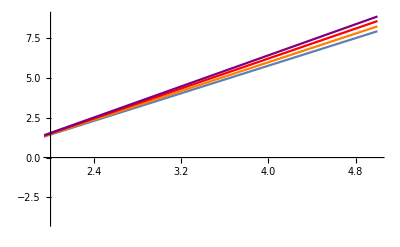

```mathematica
Block[
{qcrit,uz1,fu1,μextreme,dfu1,RGpu},
μextreme[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/uh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
qcrit[us_,uh_,μ_,z_,θ_]:=us^(θ/2-z)Sqrt[1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z))]/(μ (1-(us/uh)^(z-θ)));
uz1[q_,us_,uh_,μ_,z_,θ_]:=NDSolveValue[
{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) (((-2-z+θ) u[t]^(3-2 z) (u[t]/uh)^(z-θ))/uh^2-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(3-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(3-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)+(2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+((-((2+z-θ) (u[t]/uh)^(1+z-θ))/uh-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(1+2 z-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(1+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)) u'[t]^2)/(-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^(3-2 z) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]== us,u'[0]==0},u,{t,0.1,5.7},Method->"ExplicitRungeKutta"
];
fu1[t_,q_,us_,uh_,μ_,z_,θ_]:=uz1[q,us,uh,μ,z,θ][t];
dfu1[t_,q_,us_,uh_,μ_,z_,θ_]:=D[uz1[q,us,uh,μ,z,θ][t1],t1]/.{t1->t};
RGpu[t_,q_,us_,uh_,μ_,z_,θ_]:=Block[
{β,du,u,fu},
du=dfu1[t,q,us,uh,μ,z,θ];
u=fu1[t,q,us,uh,μ,z,θ];
fu=1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z));
β=1/(-((us/uh)^(1+z-θ) (2+z-θ))/uh+(uh^(-2 z+2 θ) us^(-1+2 (1+z-θ)) (1-(us/uh)^(-z+θ)) (z-θ) (1+z-θ) μ^2)/(2-θ)-(uh^(-1-2 z+2 θ) us^(2 (1+z-θ)) (us/uh)^(-1-z+θ) (z-θ) (-z+θ) μ^2)/(2 (2-θ)));
Return[β u^(θ/2-1)du/(fu Sqrt[u^(2(1-z))fu - du^2/fu])];
];
Show[
ListLinePlot[Table[{i,-(Abs[RGpu[i,0.4qcrit[0.1,1,0.75μextreme[1,1.50,1],1.50,1],0.1,1,0.75μextreme[1,1.50,1],1.50,1]]//Log)},{i,0.1,5,0.05}]],
ListLinePlot[Table[{i,-(Abs[RGpu[i,0.4qcrit[0.1,1,0.75μextreme[1,1.58,1],1.58,1],0.1,1,0.75μextreme[1,1.58,1],1.58,1]]//Log)},{i,0.1,5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,-(Abs[RGpu[i,0.4qcrit[0.1,1,0.75μextreme[1,1.67,1],1.67,1],0.1,1,0.75μextreme[1,1.67,1],1.67,1]]//Log)},{i,0.1,5,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,-(Abs[RGpu[i,0.4qcrit[0.1,1,0.75μextreme[1,1.75,1],1.75,1],0.1,1,0.75μextreme[1,1.75,1],1.75,1]]//Log)},{i,0.1,5,0.05}],PlotStyle->Purple],
PlotRange->{{2,5},All},AxesOrigin->{2,0}
]
]
```

NDSolveValue::ndstf: At t == 5.17056, system appears to be stiff. Methods Automatic, BDF, or StiffnessSwitching may be more appropriate.

General::stop: Further output of NDSolveValue::ndstf will be suppressed during this calculation.

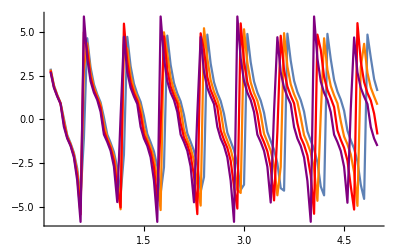

```mathematica
Block[
{qcrit,uz1,fu1,μextreme,dfu1,RGpu},
μextreme[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/uh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
qcrit[us_,uh_,μ_,z_,θ_]:=us^(θ/2-z)Sqrt[1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z))]/(μ (1-(us/uh)^(z-θ)));
uz1[q_,us_,uh_,μ_,z_,θ_]:=NDSolveValue[
{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) (((-2-z+θ) u[t]^(3-2 z) (u[t]/uh)^(z-θ))/uh^2-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(3-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(3-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)+(2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+((-((2+z-θ) (u[t]/uh)^(1+z-θ))/uh-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(1+2 z-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(1+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)) u'[t]^2)/(-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^(3-2 z) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]== us,u'[0]==0},u,{t,0.1,5.7},Method->"ExplicitRungeKutta"
];
fu1[t_,q_,us_,uh_,μ_,z_,θ_]:=uz1[q,us,uh,μ,z,θ][t];
dfu1[t_,q_,us_,uh_,μ_,z_,θ_]:=D[uz1[q,us,uh,μ,z,θ][t1],t1]/.{t1->t};
RGpu[t_,q_,us_,uh_,μ_,z_,θ_]:=Block[
{β,du,u,fu},
du=dfu1[t,q,us,uh,μ,z,θ];
u=fu1[t,q,us,uh,μ,z,θ];
fu=1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z));
β=1/(-((us/uh)^(1+z-θ) (2+z-θ))/uh+(uh^(-2 z+2 θ) us^(-1+2 (1+z-θ)) (1-(us/uh)^(-z+θ)) (z-θ) (1+z-θ) μ^2)/(2-θ)-(uh^(-1-2 z+2 θ) us^(2 (1+z-θ)) (us/uh)^(-1-z+θ) (z-θ) (-z+θ) μ^2)/(2 (2-θ)));
Return[u^(θ/2-1)du/(fu Sqrt[u^(2(1-z))fu - du^2/fu])];
];
Show[
ListLinePlot[Table[{i,Re[RGpu[i,1.5qcrit[0.1,1,0.75μextreme[1,2.00,1],2.00,1],0.1,1,0.75μextreme[1,2.00,1],2.00,1]]},{i,0.1,5,0.05}]],
ListLinePlot[Table[{i,Re[RGpu[i,1.5qcrit[0.1,1,0.75μextreme[1,2.05,1],2.05,1],0.1,1,0.75μextreme[1,2.05,1],2.05,1]]},{i,0.1,5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Re[RGpu[i,1.5qcrit[0.1,1,0.75μextreme[1,2.10,1],2.10,1],0.1,1,0.75μextreme[1,2.10,1],2.10,1]]},{i,0.1,5,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Re[RGpu[i,1.5qcrit[0.1,1,0.75μextreme[1,2.15,1],2.15,1],0.1,1,0.75μextreme[1,2.15,1],2.15,1]]},{i,0.1,5,0.05}],PlotStyle->Purple],
PlotRange->{{0.1,5},All},AxesOrigin->{0,0}
]
]
```

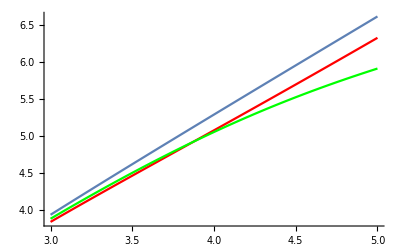

```mathematica
Block[
{qcrit,uz1,fu1,μextreme,dfu1,RGpu},
μextreme[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/uh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
qcrit[us_,uh_,μ_,z_,θ_]:=us^(θ/2-z)Sqrt[1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z))]/(μ (1-(us/uh)^(z-θ)));
uz1[q_,us_,uh_,μ_,z_,θ_]:=NDSolveValue[
{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) (((-2-z+θ) u[t]^(3-2 z) (u[t]/uh)^(z-θ))/uh^2-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(3-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(3-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)+(2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+((-((2+z-θ) (u[t]/uh)^(1+z-θ))/uh-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(1+2 z-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(1+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)) u'[t]^2)/(-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^(3-2 z) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]== us,u'[0]==0},u,{t,0.1,5.7}
];
fu1[t_,q_,us_,uh_,μ_,z_,θ_]:=uz1[q,us,uh,μ,z,θ][t];
dfu1[t_,q_,us_,uh_,μ_,z_,θ_]:=D[uz1[q,us,uh,μ,z,θ][t1],t1]/.{t1->t};
RGpu[t_,q_,us_,uh_,μ_,z_,θ_]:=Block[
{β,du,u,fu},
du=dfu1[t,q,us,uh,μ,z,θ];
u=fu1[t,q,us,uh,μ,z,θ];
fu=1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z));
β=1/(-((us/uh)^(1+z-θ) (2+z-θ))/uh+(uh^(-2 z+2 θ) us^(-1+2 (1+z-θ)) (1-(us/uh)^(-z+θ)) (z-θ) (1+z-θ) μ^2)/(2-θ)-(uh^(-1-2 z+2 θ) us^(2 (1+z-θ)) (us/uh)^(-1-z+θ) (z-θ) (-z+θ) μ^2)/(2 (2-θ)));
Return[u^(θ/2-1)du/(fu Sqrt[u^(2(1-z))fu - du^2/fu])];
];
Show[
ListLinePlot[Table[{i,-(Abs[RGpu[i,0.80qcrit[0.1,1,0.75μextreme[1,1,0],1,0],0.1,1,0.75μextreme[1,1,0],1,0]]//Log)},{i,3,5,0.05}]],
ListLinePlot[Table[{i,-(Abs[RGpu[i,0.98qcrit[0.1,1,0.75μextreme[1,1,0],1,0],0.1,1,0.75μextreme[1,1,0],1,0]]//Log)},{i,3,5,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,-(Abs[RGpu[i,0.9955qcrit[0.1,1,0.75μextreme[1,1,0],1,0],0.1,1,0.75μextreme[1,1,0],1,0]]//Log)},{i,3,5,0.05}],PlotStyle->Green],
PlotRange->{{3,5},All},AxesOrigin->{3,0}
]
]
```

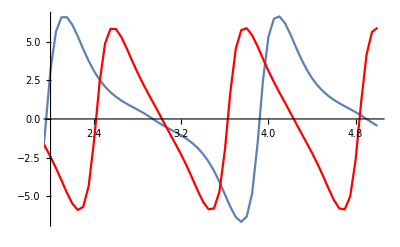

```mathematica
Block[
{qcrit,uz1,fu1,μextreme,dfu1,RGpu},
μextreme[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/uh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
qcrit[us_,uh_,μ_,z_,θ_]:=us^(θ/2-z)Sqrt[1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z))]/(μ (1-(us/uh)^(z-θ)));
uz1[q_,us_,uh_,μ_,z_,θ_]:=NDSolveValue[
{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) (((-2-z+θ) u[t]^(3-2 z) (u[t]/uh)^(z-θ))/uh^2-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(3-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(3-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)+(2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+((-((2+z-θ) (u[t]/uh)^(1+z-θ))/uh-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(1+2 z-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(1+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)) u'[t]^2)/(-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^(3-2 z) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]== us,u'[0]==0},u,{t,0.1,5.7}
];
fu1[t_,q_,us_,uh_,μ_,z_,θ_]:=uz1[q,us,uh,μ,z,θ][t];
dfu1[t_,q_,us_,uh_,μ_,z_,θ_]:=D[uz1[q,us,uh,μ,z,θ][t1],t1]/.{t1->t};
RGpu[t_,q_,us_,uh_,μ_,z_,θ_]:=Block[
{β,du,u,fu},
du=dfu1[t,q,us,uh,μ,z,θ];
u=fu1[t,q,us,uh,μ,z,θ];
fu=1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z));
β=1/(-((us/uh)^(1+z-θ) (2+z-θ))/uh+(uh^(-2 z+2 θ) us^(-1+2 (1+z-θ)) (1-(us/uh)^(-z+θ)) (z-θ) (1+z-θ) μ^2)/(2-θ)-(uh^(-1-2 z+2 θ) us^(2 (1+z-θ)) (us/uh)^(-1-z+θ) (z-θ) (-z+θ) μ^2)/(2 (2-θ)));
Return[u^(θ/2-1)du/(fu Sqrt[u^(2(1-z))fu - du^2/fu])];
];
Show[
ListLinePlot[Table[{i,Re[RGpu[i,1.4qcrit[0.1,1,0.75μextreme[1,1,0],1,0],0.1,1,0.75μextreme[1,1,0],1,0]]},{i,0.1,5,0.05}]],
ListLinePlot[Table[{i,Re[RGpu[i,2.1qcrit[0.1,1,0.75μextreme[1,1,0],1,0],0.1,1,0.75μextreme[1,1,0],1,0]]},{i,0.1,5,0.05}],PlotStyle->Red],
PlotRange->{{2,5},All},AxesOrigin->{2,0}
]
]
```